The n-cube Q_n(n ≥1)  is the graph whose vertex set is the set of all n-tuples of 0s and 1s, where two n-tuples are adjacent if they differ in precisely one coordinate.

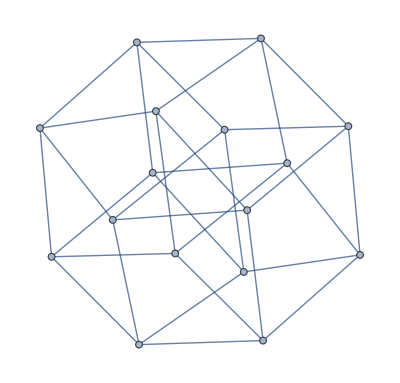

```mathematica
n=4;
Graph[UndirectedEdge@@#&/@Select[Subsets[Tuples[{0,1},n],{2}],Norm[#[[1]]-#[[2]]]==1&]]
```

Q_n都是二部图，因为可以将其分成这样的两部分：

V_1={v|∑_(k∈v) k is odd,v∈V(Q_n)},V_2={v|∑_(k∈v) k is even,v∈V(Q_n)}.

```mathematica
BipartiteGraphQ[%]
```

True

顶点数和边数：

```mathematica
v(Subscript[Q, n])=2^n,e(Subscript[Q, n])=n (2^(n-1)).
```